```mathematica
m[k_,τ_]:=m/.Solve[k==m*Exp[-m*τ],m][[1]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

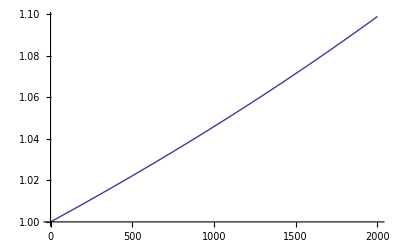

```mathematica
Plot[m[k,42.9*^-6]/k,{k,0,2000}]
```

```mathematica
data=Table[{k, m[k,42.9*^-6]/k},{k,0,2000,1}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

```mathematica
SetDirectory[NotebookDirectory[]];
Export["totzeitkorrektur.tsv", data];
```